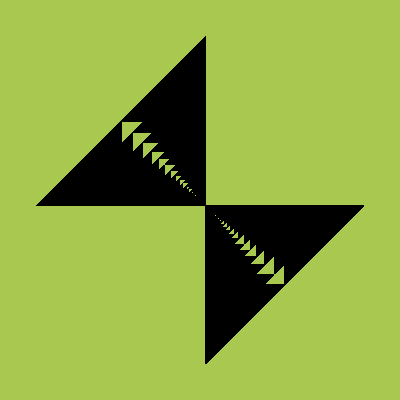
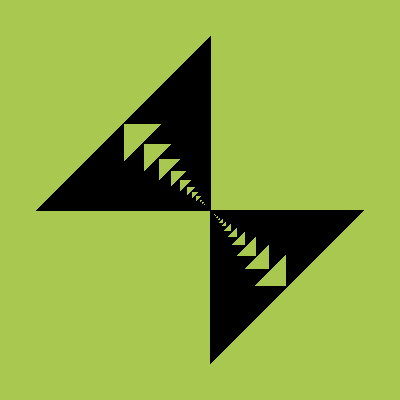
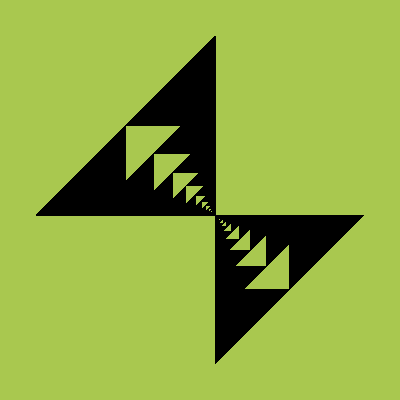
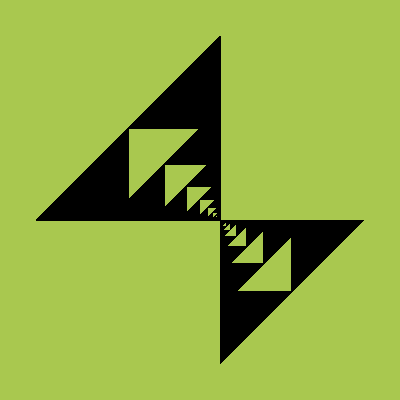
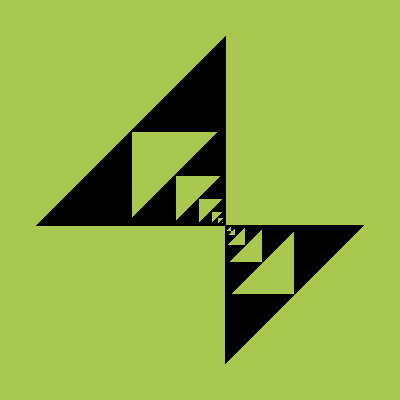
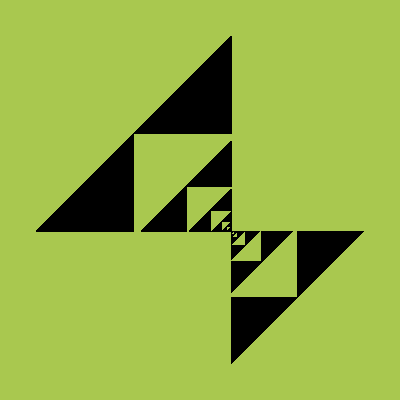
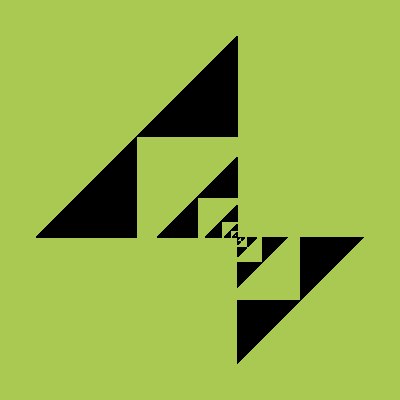
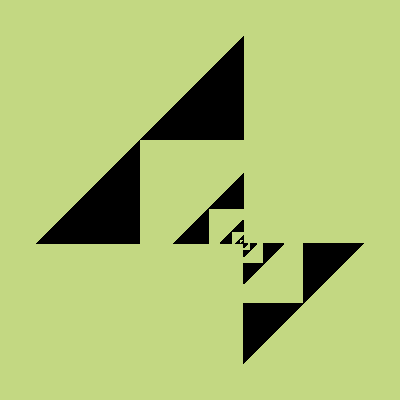

dlji.gif

Hue[a/4]

```mathematica
n=100;
T1=Developer`ToPackedArray[{{-1.,0.},{-0.5,0.},{-0.5,0.5}}];

T2=Developer`ToPackedArray[{{-0.5,0.5},{0.,0.5},{0.,1.}}];
g=Table[Graphics[{Polygon[Table[a^k T1,{k,0,n}]],Polygon[Table[a^k T2,{k,0,n}]]},Background->ColorData["IslandColors",(a^2+0.1)*2]],{a,-0.93,0.5,0.05}]
Export["dlji.gif",g,"DisplayDurations"->0.15,ImageResolution->500]

Hue[a/4]
```